```mathematica
v =Table[{j,i},{i,2,-2,-1},{j,-2,2}]
A = Transpose[({{1/2, -1/3}, {3/4, 1/2}})]
```

{{{-2,2},{-1,2},{0,2},{1,2},{2,2}},{{-2,1},{-1,1},{0,1},{1,1},{2,1}},{{-2,0},{-1,0},{0,0},{1,0},{2,0}},{{-2,-1},{-1,-1},{0,-1},{1,-1},{2,-1}},{{-2,-2},{-1,-2},{0,-2},{1,-2},{2,-2}}}

{{1/2,3/4},{-1/3,1/2}}

```mathematica
V = v//MatrixForm
```

((-2
2) | (-1
2) | (0
2) | (1
2) | (2
2)
(-2
1) | (-1
1) | (0
1) | (1
1) | (2
1)
(-2
0) | (-1
0) | (0
0) | (1
0) | (2
0)
(-2
-1) | (-1
-1) | (0
-1) | (1
-1) | (2
-1)
(-2
-2) | (-1
-2) | (0
-2) | (1
-2) | (2
-2))

```mathematica
A.V//MatrixForm
```

{{1/2,3/4},{-1/3,1/2}}.((-2
2) | (-1
2) | (0
2) | (1
2) | (2
2)
(-2
1) | (-1
1) | (0
1) | (1
1) | (2
1)
(-2
0) | (-1
0) | (0
0) | (1
0) | (2
0)
(-2
-1) | (-1
-1) | (0
-1) | (1
-1) | (2
-1)
(-2
-2) | (-1
-2) | (0
-2) | (1
-2) | (2
-2))

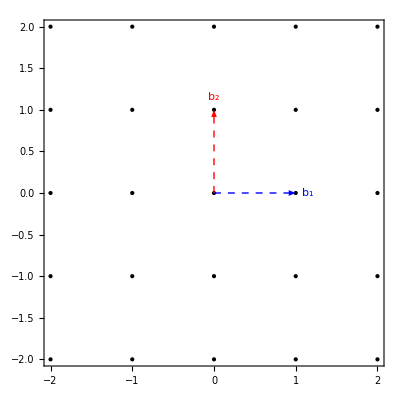

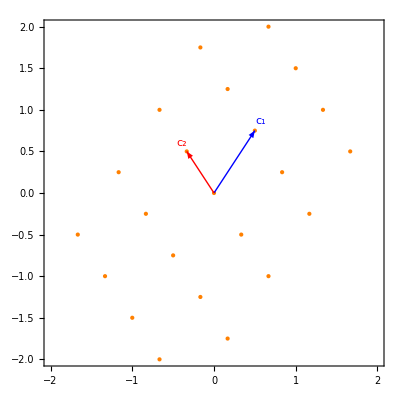

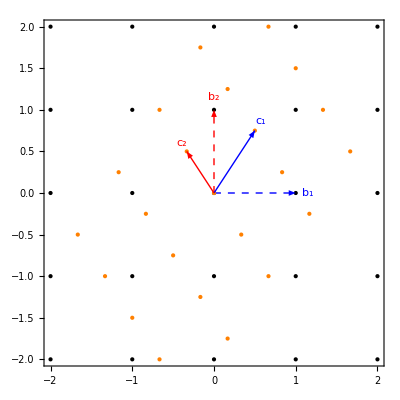

```mathematica
g1 = Graphics[{{Black,PointSize[Large],Point[  Flatten[v,1]]},{Blue,Thick,Dashed,Arrow[{{0,0},{1,0}}]},{Blue,Text[Subscript[b, 1],{1.15,0}]},{Red,Thick,Dashed,Arrow[{{0,0},{0,1}}]},{Red,Text[Subscript[b, 2],{0,1.15}]}},Frame->True,PlotRange->{{-2,2},{-2,2}}]
g2 = Graphics[{{Orange,PointSize[Large],Point[  Flatten[v.A,1]]},{Blue,Thick,Arrow[{{0,0}.A,{1,0}.A}]},{Blue,Text[Subscript[c, 1],{1.15,0}.A]},{Red,Thick,Arrow[{{0,0}.A,{0,1}.A}]},{Red,Text[Subscript[c, 2],{0,1.2}.A]}},Frame->True,PlotRange->{{-2,2},{-2,2}}]
g12=Show[g1,g2]
```

```mathematica
Export["g1.png",g1]
Export["g2.png",g2]
Export["g12.png",g12]
```

g1.png

g2.png

g12.png

```mathematica
Directory[]
```

C:\Users\SergioMuniz\Documents

```mathematica
x=({{1}, {0}}); y=({{0}, {1}});
A.x//MatrixForm
```

(1/2
3/4)

```mathematica
B=({{1/2, -1/3}, {3/4, 1/2}})
```

{{1/2,-1/3},{3/4,1/2}}

```mathematica
B.x//MatrixForm
```

(1/2
3/4)

```mathematica
B//TeXForm
```

\left(
\begin{array}{cc}
 \frac{1}{2} & -\frac{1}{3} \\
 \frac{3}{4} & \frac{1}{2} \\
\end{array}
\right)

```mathematica
B//TeXForm
```

\left(
\begin{array}{cc}
 \frac{1}{2} & -\frac{1}{3} \\
 \frac{3}{4} & \frac{1}{2} \\
\end{array}
\right)